```mathematica
7963.75 z/(6371+1.25 z)/. z->70
```

86.3145

```mathematica
86.31454672137494
```

86.3145

```mathematica
288.15-6.5*11
```

216.65

```mathematica
convert[z_]:=7963.75 z/(6371+1.25 z)
```

```mathematica
Temperature[h_]:=UnitStep[11-h]*(288.15-6.5 h) + (UnitStep[h-11]*UnitStep[20-h])*216.65 +(UnitStep[h-20]*UnitStep[32-h])*(196.65+h)+(UnitStep[h-32]*UnitStep[47-h])*(139.05+2.8h)+(UnitStep[h-47]*UnitStep[51-h])*(270.65)+(UnitStep[h-51]*UnitStep[71-h])*(413.45-2.8 h)+(UnitStep[h-71])*(356.65-2h)
```

```mathematica
Pressure[h_]:=Piecewise[{{(101325.0 (288.15/(288.15-6.5 h)) ^(34.1632/-6.5)),h<11},{(22632.06 Exp[-34.1632 (h-11)/216.65]),11≤h≤20},{(5474.889(216.65/(216.65+(h-20)))^ 34.1632),20<h<32},{(868.0187 (228.65/(228.65+2.8 (h-32))) ^(34.1632/2.8)),32≤h≤47},{(110.9063×Exp[-34.1632×(h-47)/270.65]),47<h<51},{(66.93887×(270.65/(270.65-2.8×(h-51))) ^(34.1632/ -2.8)),51≤h≤71},{(3.956420×(214.65/(214.65-2×(h-71))) ^(34.1632/ -2)),h>71}}]
```

```mathematica
Density[h_]:=Pressure[h]/Temperature[h]/287.053;
```

```mathematica
IAStoVAS[v_,z_]:=v*1852/3600/Sqrt[Density[convert[z]]];
```

```mathematica
{z,SpeedOfSound[z]}/.z->0
```

{0,340.297}

```mathematica
2×3
```

6

```mathematica
SpeedOfSound[15.0]
```

295.072

```mathematica
{z,SpeedOfSound[z]}/.Solve[convert[z]==,z][[1,1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{25.7292,303.134}

```mathematica
SpeedOfSound[z_]:=Sqrt[1.4*287.053*Temperature[convert[z]]];
```

```mathematica
Plot[Temperature[convert[h]],{h,0,70}]
```

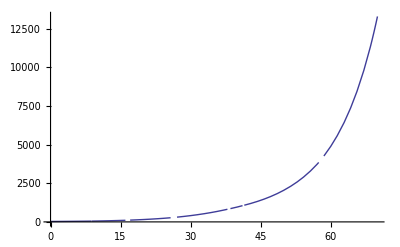

```mathematica
Plot[60*1852/3600/Sqrt[Density[convert[h]]],{h,0,70}]
```

```mathematica
ParametricPlot[{{SpeedOfSound[h],h},{2*SpeedOfSound[h],h},{3*SpeedOfSound[h],h},{IAStoVAS[60,h],h},{IAStoVAS[160,h],h},{IAStoVAS[220,h],h},{IAStoVAS[370,h],h},{IAStoVAS[430,h],h}},{h,0,70}, PlotRange->{{0,1500},{0,70}}, AspectRatio->1,Exclusions->None,GridLines->Automatic, GridLinesStyle->Directive[Dashed]]
```